# Omicron analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-countries

```mathematica
dataset="omicron-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={"Philippines"};
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-02-05

```mathematica
countries=Union[seqData[[All,2]]]
```

{Australia,Austria,Brazil,Canada,Chile,Colombia,Croatia,Denmark,France,Germany,India,Ireland,Israel,Japan,Netherlands,New Zealand,Norway,Singapore,Slovakia,South Africa,South Korea,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

```mathematica
countries=Complement[countries,countriesToDrop]
```

{Australia,Austria,Brazil,Canada,Chile,Colombia,Croatia,Denmark,France,Germany,India,Ireland,Israel,Japan,Netherlands,New Zealand,Norway,Singapore,Slovakia,South Africa,South Korea,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countryVariantCounts[country_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==country&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
countrySequenceCounts[country_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==country][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->countrySequenceCounts[#][[-15;;-1]]&,countries]
```

{Australia→{{2022-01-22,113},{2022-01-23,115},{2022-01-24,137},{2022-01-25,92},{2022-01-26,103},{2022-01-27,115},{2022-01-28,112},{2022-01-29,104},{2022-01-30,109},{2022-01-31,157},{2022-02-01,141},{2022-02-02,131},{2022-02-03,98},{2022-02-04,104},{2022-02-05,64}},Austria→{{2022-01-22,130},{2022-01-23,89},{2022-01-24,85},{2022-01-25,135},{2022-01-26,11},{2022-01-27,22},{2022-01-28,22},{2022-01-29,0},{2022-01-30,0},{2022-01-31,0},{2022-02-01,0},{2022-02-02,0},{2022-02-03,0},{2022-02-04,0},{2022-02-05,0}},Brazil→{{2022-01-22,50},{2022-01-23,13},{2022-01-24,70},{2022-01-25,50},{2022-01-26,19},{2022-01-27,10},{2022-01-28,281},{2022-01-29,0},{2022-01-30,284},{2022-01-31,234},{2022-02-01,0},{2022-02-02,0},{2022-02-03,0},{2022-02-04,0},{2022-02-05,0}},Canada→{{2022-01-22,159},{2022-01-23,113},{2022-01-24,167},{2022-01-25,142},{2022-01-26,166},{2022-01-27,74},{2022-01-28,76},{2022-01-29,32},{2022-01-30,28},{2022-01-31,1},{2022-02-01,0},{2022-02-02,0},{2022-02-03,0},{2022-02-04,0},{2022-02-05,0}},Chile→{{2022-01-22,8},{2022-01-23,22},{2022-01-24,39},{2022-01-25,39},{2022-01-26,44},{2022-01-27,18},{2022-01-28,8},{2022-01-29,24},{2022-01-30,31},{2022-01-31,18},{2022-02-01,8},{2022-02-02,0},{2022-02-03,0},{2022-02-04,0},{2022-02-05,0}},Colombia→{{2022-01-22,2},{2022-01-23,9},{2022-01-24,13},{2022-01-25,4},{2022-01-26,2},{2022-01-27,0},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0},{2022-01-31,0},{2022-02-01,0},{2022-02-02,0},{2022-02-03,0},{2022-02-04,0},{2022-02-05,0}},Croatia→{{2022-01-22,90},{2022-01-23,32},{2022-01-24,126},{2022-01-25,56},{2022-01-26,55},{2022-01-27,29},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0},{2022-01-31,0},{2022-02-01,0},{2022-02-02,0},{2022-02-03,0},{2022-02-04,0},{2022-02-05,0}},Denmark→{{2022-01-22,1928},{2022-01-23,1992},{2022-01-24,2218},{2022-01-25,2310},{2022-01-26,1487},{2022-01-27,1592},{2022-01-28,961},{2022-01-29,1341},{2022-01-30,2287},{2022-01-31,2341},{2022-02-01,493},{2022-02-02,649},{2022-02-03,1298},{2022-02-04,667},{2022-02-05,435}},France→{{2022-01-22,189},{2022-01-23,279},{2022-01-24,1480},{2022-01-25,276},{2022-01-26,216},{2022-01-27,145},{2022-01-28,162},{2022-01-29,81},{2022-01-30,110},{2022-01-31,1034},{2022-02-01,113},{2022-02-02,117},{2022-02-03,70},{2022-02-04,0},{2022-02-05,0}},Germany→{{2022-01-22,537},{2022-01-23,158},{2022-01-24,1170},{2022-01-25,1434},{2022-01-26,1247},{2022-01-27,1509},{2022-01-28,1222},{2022-01-29,577},{2022-01-30,188},{2022-01-31,919},{2022-02-01,369},{2022-02-02,175},{2022-02-03,117},{2022-02-04,10},{2022-02-05,4}},India→{{2022-01-22,89},{2022-01-23,27},{2022-01-24,149},{2022-01-25,94},{2022-01-26,67},{2022-01-27,70},{2022-01-28,58},{2022-01-29,42},{2022-01-30,31},{2022-01-31,79},{2022-02-01,25},{2022-02-02,61},{2022-02-03,108},{2022-02-04,0},{2022-02-05,0}},Ireland→{{2022-01-22,29},{2022-01-23,28},{2022-01-24,30},{2022-01-25,0},{2022-01-26,0},{2022-01-27,0},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0},{2022-01-31,0},{2022-02-01,0},{2022-02-02,0},{2022-02-03,0},{2022-02-04,0},{2022-02-05,0}},Israel→{{2022-01-22,284},{2022-01-23,212},{2022-01-24,477},{2022-01-25,595},{2022-01-26,267},{2022-01-27,1057},{2022-01-28,365},{2022-01-29,54},{2022-01-30,592},{2022-01-31,177},{2022-02-01,60},{2022-02-02,2},{2022-02-03,0},{2022-02-04,0},{2022-02-05,0}},Japan→{{2022-01-22,27},{2022-01-23,11},{2022-01-24,27},{2022-01-25,20},{2022-01-26,9},{2022-01-27,30},{2022-01-28,14},{2022-01-29,9},{2022-01-30,2},{2022-01-31,6},{2022-02-01,1},{2022-02-02,2},{2022-02-03,5},{2022-02-04,0},{2022-02-05,0}},Netherlands→{{2022-01-22,256},{2022-01-23,223},{2022-01-24,203},{2022-01-25,125},{2022-01-26,117},{2022-01-27,93},{2022-01-28,91},{2022-01-29,68},{2022-01-30,61},{2022-01-31,51},{2022-02-01,30},{2022-02-02,14},{2022-02-03,9},{2022-02-04,0},{2022-02-05,0}},New Zealand→{{2022-01-22,30},{2022-01-23,43},{2022-01-24,50},{2022-01-25,35},{2022-01-26,52},{2022-01-27,59},{2022-01-28,106},{2022-01-29,36},{2022-01-30,11},{2022-01-31,17},{2022-02-01,6},{2022-02-02,24},{2022-02-03,4},{2022-02-04,0},{2022-02-05,0}},Norway→{{2022-01-22,31},{2022-01-23,85},{2022-01-24,30},{2022-01-25,97},{2022-01-26,18},{2022-01-27,18},{2022-01-28,14},{2022-01-29,10},{2022-01-30,73},{2022-01-31,36},{2022-02-01,101},{2022-02-02,12},{2022-02-03,12},{2022-02-04,0},{2022-02-05,0}},Singapore→{{2022-01-22,42},{2022-01-23,31},{2022-01-24,41},{2022-01-25,29},{2022-01-26,16},{2022-01-27,23},{2022-01-28,22},{2022-01-29,21},{2022-01-30,17},{2022-01-31,24},{2022-02-01,18},{2022-02-02,19},{2022-02-03,0},{2022-02-04,0},{2022-02-05,0}},Slovakia→{{2022-01-22,58},{2022-01-23,21},{2022-01-24,17},{2022-01-25,10},{2022-01-26,99},{2022-01-27,12},{2022-01-28,26},{2022-01-29,3},{2022-01-30,3},{2022-01-31,13},{2022-02-01,13},{2022-02-02,105},{2022-02-03,5},{2022-02-04,0},{2022-02-05,0}},South Africa→{{2022-01-22,9},{2022-01-23,8},{2022-01-24,44},{2022-01-25,3},{2022-01-26,8},{2022-01-27,7},{2022-01-28,11},{2022-01-29,22},{2022-01-30,4},{2022-01-31,5},{2022-02-01,7},{2022-02-02,3},{2022-02-03,12},{2022-02-04,0},{2022-02-05,0}},South Korea→{{2022-01-22,0},{2022-01-23,0},{2022-01-24,0},{2022-01-25,0},{2022-01-26,0},{2022-01-27,0},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0},{2022-01-31,0},{2022-02-01,0},{2022-02-02,0},{2022-02-03,0},{2022-02-04,0},{2022-02-05,0}},Spain→{{2022-01-22,62},{2022-01-23,126},{2022-01-24,256},{2022-01-25,214},{2022-01-26,194},{2022-01-27,99},{2022-01-28,164},{2022-01-29,59},{2022-01-30,26},{2022-01-31,73},{2022-02-01,16},{2022-02-02,22},{2022-02-03,19},{2022-02-04,0},{2022-02-05,0}},Sweden→{{2022-01-22,38},{2022-01-23,119},{2022-01-24,225},{2022-01-25,161},{2022-01-26,110},{2022-01-27,97},{2022-01-28,67},{2022-01-29,33},{2022-01-30,70},{2022-01-31,91},{2022-02-01,47},{2022-02-02,8},{2022-02-03,1},{2022-02-04,0},{2022-02-05,0}},Switzerland→{{2022-01-22,138},{2022-01-23,395},{2022-01-24,680},{2022-01-25,664},{2022-01-26,372},{2022-01-27,203},{2022-01-28,138},{2022-01-29,172},{2022-01-30,138},{2022-01-31,396},{2022-02-01,133},{2022-02-02,163},{2022-02-03,26},{2022-02-04,0},{2022-02-05,0}},Thailand→{{2022-01-22,0},{2022-01-23,0},{2022-01-24,24},{2022-01-25,12},{2022-01-26,11},{2022-01-27,0},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0},{2022-01-31,0},{2022-02-01,0},{2022-02-02,0},{2022-02-03,0},{2022-02-04,0},{2022-02-05,0}},United Kingdom→{{2022-01-22,7414},{2022-01-23,7528},{2022-01-24,10379},{2022-01-25,8240},{2022-01-26,7469},{2022-01-27,5499},{2022-01-28,5703},{2022-01-29,6106},{2022-01-30,7163},{2022-01-31,9056},{2022-02-01,4986},{2022-02-02,8747},{2022-02-03,6378},{2022-02-04,4859},{2022-02-05,4913}},USA→{{2022-01-22,4424},{2022-01-23,3213},{2022-01-24,6223},{2022-01-25,5204},{2022-01-26,4273},{2022-01-27,3786},{2022-01-28,2509},{2022-01-29,1613},{2022-01-30,825},{2022-01-31,1880},{2022-02-01,1301},{2022-02-02,939},{2022-02-03,1068},{2022-02-04,0},{2022-02-05,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[country_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==country,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.00001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{logitTransform[0.0005],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[country_]:=Map[logisticPrevSeries[countryVariantCounts[country,#],countrySequenceCounts[country]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForCountries=Map[freqForCountry,countries];
```

```mathematica
modeledFreqsForCountries=Map[{modeledLogisticPrevSeries[logisticPrevSeries[countryVariantCounts[#,"Omicron"],countrySequenceCounts[#]]]}&,countries];
```

```mathematica
legendsForCountries=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForCountries];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-countries_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-countries_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[country_,variant_]:=Module[{countryVariantFrequencyDateSeries,countryCasesDateSeries,tuples},
countryVariantFrequencyDateSeries=smoothedPrevalence[countryVariantCounts[country,variant],countrySequenceCounts[country]];
countryCasesDateSeries=csGather[country];
tuples=compareWithDate[countryVariantFrequencyDateSeries,countryCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
panels=Map[splitCasePlot,countries];
```

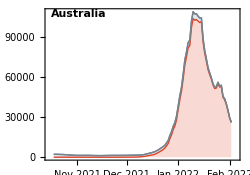
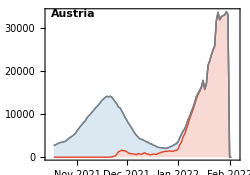
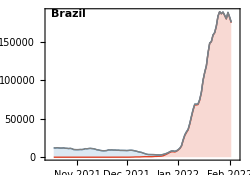
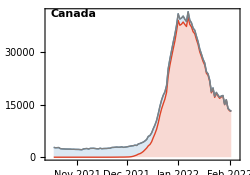
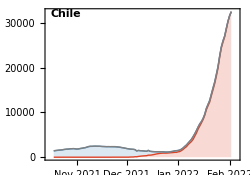
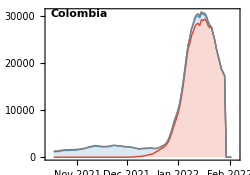
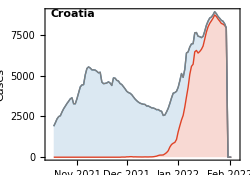
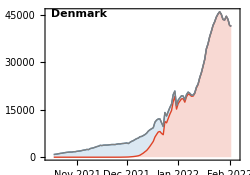
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=500000;
```

```mathematica
splitCaseLogPlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[country_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[country_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[country,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->200,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{50,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.88,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForCountries=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,countries];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{countries,legendsForCountries}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-log-cases.png